Initialize functions

```mathematica
(*Ensure that variables are defined globally*)
SetOptions[EvaluationNotebook[],CellContext->"Global`"]
NotebookOpen[NotebookDirectory[]<>"GB-strain-scattering_init.nb"];
NotebookEvaluate[NotebookDirectory[]<>"GB-strain-scattering_init.nb"];
```

Import data

```mathematica
(*Si, pc: Wang 2011 (Figure 2 550(99%)), sc: Glassbrenner 1964*)
κLdataSipc=Import[NotebookDirectory[]<>"../Literature_Data/Si-pc_Wang-Fig2.csv","CSV"];
κLdataSisc=Import[NotebookDirectory[]<>"../Literature_Data/Si-sc_Glassbrenner.csv","CSV"];
κLdataSisc=Table[{κLdataSisc[[i,1]],100/κLdataSisc[[i,2]]},{i,2,Length[κLdataSisc]}];

(*AlN, Watari 2002 (Figure 2, ceramic B and pure single crystal)*)
κLdataAlNpc=Import[NotebookDirectory[]<>"../Literature_Data/AlN-pc_Watari-Fig3.csv","CSV"];
κLdataAlNsc=Import[NotebookDirectory[]<>"../Literature_Data/AlN-sc_Watari-Fig3.csv","CSV"];

(*Al2O3, pc: Berman 1952 (Figure 1, sintered alumina), sc: Berman 1951 (Figure 5, artificial sapphire)*)
κLdataAl2O3pc=Import[NotebookDirectory[]<>"../Literature_Data/Al2O3-pc_Berman-1952.csv","CSV"];
κLdataAl2O3pc=Table[{κLdataAl2O3pc[[i,1]],100*κLdataAl2O3pc[[i,2]]},{i,1,Length[κLdataAl2O3pc]}];
κLdataAl2O3sc=Import[NotebookDirectory[]<>"../Literature_Data/Al2O3-sc_Berman-1951.csv","CSV"];
κLdataAl2O3sc=Table[{κLdataAl2O3sc[[i,1]],100*κLdataAl2O3sc[[i,2]]},{i,1,Length[κLdataAl2O3sc]}];
```

Modeling polycrystalline Si

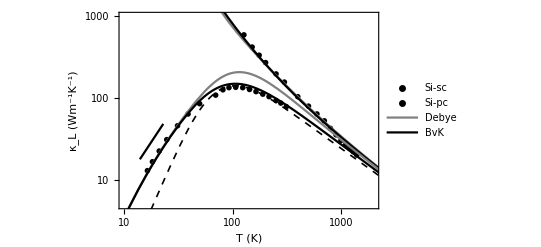

```mathematica
(*#############################*)
(*### Material values for Si ###*)
(*#############################*)

(*#### crystal properties ####*)
vs=6084. (*[m/s] average speed of sound*);
V=2*10^-29 (*[m^3]volume of atom*);
n=2(*# atoms per primitive unit cell (N in paper)*);
γ=1(*Grun parameter*);
ν=0.27(*Poisson's ratio*);
kmax=k0[V*n]//N(*[m^-1] edge of FBZ*);
ωD=vs kmax (*[s^-1] Debye frequency*);
ωmax=ω0[vs,V*n](*[s^-1] max frequency for BvK*);

(*#### phonon-phonon (from Wang et al.)####*)
C1=2.69*10^-19 (*[s/K]*);
C1BvK=1.53*10^-19(*[s/K]*);
C2=167(*[K]*);;
C2BvK=140(*[K]*);

(*#### point defect (from Wang et al.)####*)
C3=1.81*10^-45(*[s^3]*);
C3BvK=1.69*10^-45 (*[s^3]*);

(*#### microstructure ####*)
b=(V n)^(1/3)(*[m] Burger's vector (bGB in paper)*);
dGS=350*10^-9(*[m] average grain size*);
n1D=3/dGS//N(*[m^-1] number density of GBs *);
d=3*10^-9 (*[m] GB dislocation spacing (D in paper)*);

Show[ListLogLogPlot[{κLdataSisc,κLdataSipc},
PlotRange->{{10,2000},{5,1000}},
FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,0,3}],Automatic},{Automatic,Automatic}},
FrameLabel->{Style["T (K)"],Style["κ_L (Wm^-1K^-1)",SingleLetterItalics->False]},
PlotMarkers->{{◻,18},{◼,18}},
PlotLegends->Placed[PointLegend[{Style["Si-sc",15,FontFamily->"Times New Roman"],Style["Si-pc",15,FontFamily->"Times New Roman"]},Spacings->0.1],{0.85,0.87}]],
LogLogPlot[{κL[T,(τppModel[ω,T,C1,C2]^-1+τPD[ω,C3]^-1)^-1,vs,ω/vs,{ω,0,ωD}],
κL[T,(τppModel[ω,T,C1BvK,C2BvK]^-1+τPD[ω,C3BvK]^-1)^-1,vgBvK[kωBvK[ω,ωmax,kmax],ωmax,kmax],kωBvK[ω,ωmax,kmax],{ω,0,ωmax}],κL[T,(τinvEmp[ω,d,b,n1D]+τppModel[ω,T,C1,C2]^-1+τPD[ω,C3]^-1)^-1,vs,ω/vs,{ω,0,ωD}],κL[T,(τppModel[ω,T,C1BvK,C2BvK]^-1+τinvEmp[ω,d,b,n1D]+τPD[ω,C3BvK]^-1)^-1,vgBvK[kωBvK[ω,ωmax,kmax],ωmax,kmax],kωBvK[ω,ωmax,kmax],{ω,0,ωmax}],
κL[T,(τppModel[ω,T,C1BvK,C2BvK]^-1+τPD[ω,C3BvK]^-1+vgBvK[kωBvK[ω,ωmax,kmax],ωmax,kmax]/(0.7*10^-6))^-1,vgBvK[kωBvK[ω,ωmax,kmax],ωmax,kmax],kωBvK[ω,ωmax,kmax],{ω,0,ωmax}]},{T,1,5000},
PlotStyle->{Gray,Black,Gray,Black,Directive[Dashed,Black,Thickness->0.003]},
PlotLegends->Placed[LineLegend[{Style["Debye",13,FontFamily->"Times New Roman"],Style["BvK",13,FontFamily->"Times New Roman"]},Spacings->0.2],{0.13,0.89}]],
ListLogLogPlot[{T2[18,{Tref,14,23}]},Joined->True]]
```

Modeling polycrystalline AlN

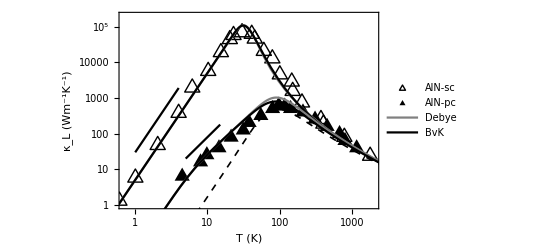

```mathematica
(*#######################*)
(*#### values for AlN ####*)
(*#######################*)

(*#### crystal parameters ####*)
vs=6976. ;
V=1.04*10^-29 ;
n=4;
kmax=k0[V*n]//N;
ωD=vs kmax;
ωmax=ω0[vs,V*n];
γ=1.1;
ν=0.2 ;

(*#### phonon-phonon scattering ####*)
C1=2.2*10^-19;
C1BvK=1.3*10^-19;
C2=270;
C2BvK=250;

(*#### microstructure ####*)
Casmir=6*10^-3;
dGS=1.*10^-6;
n1D=3/dGS//N;
d=8.*10^-9;
b=(V*n)^(1/3);

Show[ListLogLogPlot[{κLdataAlNsc,κLdataAlNpc},
PlotRange->{{0.7,2000},{1,2*10^5}},
FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,0,5}],Automatic},{Automatic,Automatic}},
FrameLabel->{Style["T (K)"],Style["κ_L (Wm^-1K^-1)",SingleLetterItalics->False]},
PlotMarkers->{{△,18},{▲,18}},
PlotLegends->Placed[PointLegend[{Style["AlN-sc",15,FontFamily->"Times New Roman"],Style["AlN-pc",15,FontFamily->"Times New Roman"]},Spacings->0.1],{0.85,0.87}]],
LogLogPlot[{κL[T,(τppModel[ω,T,C1,C2]^-1+vs/Casmir)^-1,vs,ω/vs,{ω,0,ωD}],κL[T,(τppModel[ω,T,C1BvK,C2BvK]^-1+vgBvK[kωBvK[ω,ωmax,kmax],ωmax,kmax]/Casmir)^-1,vgBvK[kωBvK[ω,ωmax,kmax],ωmax,kmax],kωBvK[ω,ωmax,kmax],{ω,0,ωmax}]},{T,.1,5000},
PlotStyle->{Gray,Black}],
LogLogPlot[{κL[T,(τinvEmp[ω,d,b,n1D]+τppModel[ω,T,C1,C2]^-1)^-1,vs,ω/vs,{ω,0,ωD}],κL[T,(τppModel[ω,T,C1BvK,C2BvK]^-1+τinvEmp[ω,d,b,n1D])^-1,vgBvK[kωBvK[ω,ωmax,kmax],ωmax,kmax],kωBvK[ω,ωmax,kmax],{ω,0,ωmax}],κL[T,(τppModel[ω,T,C1BvK,C2BvK]^-1+vgBvK[kωBvK[ω,ωmax,kmax],ωmax,kmax]/(2*10^-6))^-1,vgBvK[kωBvK[ω,ωmax,kmax],ωmax,kmax],kωBvK[ω,ωmax,kmax],{ω,0,ωmax}]},{T,.1,5000},PlotStyle->{Gray,Black,Directive[Dashed,Black,Thickness->0.003]},
PlotLegends->Placed[LineLegend[{Style["Debye",13,FontFamily->"Times New Roman"],Style["BvK",13,FontFamily->"Times New Roman"]},Spacings->0.2],{0.13,0.89}]],
ListLogLogPlot[{T2[20,{Tref,5,15}],T3[30,{Tref,1,4}]},Joined->True]]
```

Modeling polycrystalline Al_2 O_3

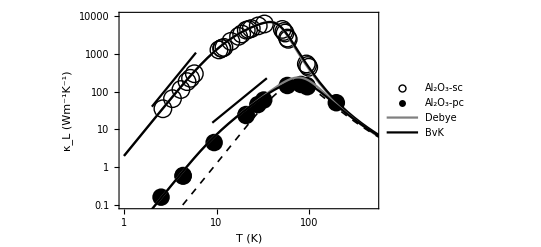

```mathematica
(*#########################*)
(*#### values for Al2O3 ####*)
(*#########################*)

(*#### crystal properties ####*)
vs=7011. ;
V=8.5*10^-30 ;
n=10;
kmax=k0[V*n]//N;
ωD=vs kmax;
ωmax=ω0[vs,V*n];
γ=1.3;
ν=0.23;

(*#### phonon-phonon ####*)
C1=30*10^-19 ;
C1BvK=15*10^-19;
C2=350 ;
C2BvK=320;

(*#### point defect ####*)
C3=1*10^-45;
C3BvK=1*10^-45;

(*#### microstructure ####*)
b=(V*n)^(1/3);
Casmir=2.4*10^-3;
dGS=1*10^-6;
n1D=3/dGS//N;
d=5.5*10^-9;

Show[ListLogLogPlot[{κLdataAl2O3sc,κLdataAl2O3pc},
PlotRange->{{1,500},{10^-1,10^4}},
FrameTicks->{{Table[{10^k,Superscript[10,k]},{k,-1,4}],Automatic},{Automatic,Automatic}},
FrameLabel->{Style["T (K)"],Style["κ_L (Wm^-1K^-1)",SingleLetterItalics->False]},
PlotMarkers->{{◦,18},{•,18}},
PlotLegends->Placed[PointLegend[{Style["Al_2O_3-sc",15,FontFamily->"Times New Roman",SingleLetterItalics->False],Style["Al_2O_3-pc",15,FontFamily->"Times New Roman",SingleLetterItalics->False]},Spacings->0.1],{0.82,0.15}]],
LogLogPlot[{κL[T,(τppModel[ω,T,C1,C2]^-1+τPD[ω,C3]^-1+vs/Casmir)^-1,vs,ω/vs,{ω,0,ωD}],κL[T,(τppModel[ω,T,C1BvK,C2BvK]^-1+τPD[ω,C3BvK]^-1+vgBvK[kωBvK[ω,ωmax,kmax],ωmax,kmax]/Casmir)^-1,vgBvK[kωBvK[ω,ωmax,kmax],ωmax,kmax],kωBvK[ω,ωmax,kmax],{ω,0,ωmax}],κL[T,(τppModel[ω,T,C1,C2]^-1+τPD[ω,C3]^-1+τinvEmp[ω,d,b,n1D])^-1,vs,ω/vs,{ω,0,ωD}],κL[T,(τppModel[ω,T,C1BvK,C2BvK]^-1+τPD[ω,C3BvK]^-1+τinvEmp[ω,d,b,n1D])^-1,vgBvK[kωBvK[ω,ωmax,kmax],ωmax,kmax],kωBvK[ω,ωmax,kmax],{ω,0,ωmax}],κL[T,(τppModel[ω,T,C1BvK,C2BvK]^-1+τPD[ω,C3BvK]^-1+vgBvK[kωBvK[ω,ωmax,kmax],ωmax,kmax]/(1.5*10^-6))^-1,vgBvK[kωBvK[ω,ωmax,kmax],ωmax,kmax],kωBvK[ω,ωmax,kmax],{ω,0,ωmax}]},{T,1,5000},
PlotStyle->{Gray,Black,Gray,Black,Directive[Dashed,Black,Thickness->0.003]},
PlotLegends->Placed[LineLegend[{Style["Debye",13,FontFamily->"Times New Roman"],Style["BvK",13,FontFamily->"Times New Roman"]},Spacings->0.2],{0.13,0.89}]],
ListLogLogPlot[{T2[15,{Tref,9,35}],T3[40,{Tref,2,6}]},Joined->True]]
```